# First test

```mathematica
(* ================================================================ *)
(* KL_Pr_vs_k.wl                                                    *)
(* KL divergence of the empirical P(r) vs. COE and Poisson          *)
(* references, as a function of kick strength k.                    *)
(* Requires: QKT_full.wl in the same directory.                     *)
(* ================================================================ *)

(* === SETUP === *)
SetDirectory[NotebookDirectory[]];
LaunchKernels[14];
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\QKT_full.wl"];
```

```mathematica
(* === PARAMETERS === *)
J      = 500;
alpha  = 0.84;
nBins  = 100;                              (* histogram bins on [0,1] *)
```

```mathematica
kList=Range[10,30.,0.1];
```

```mathematica
(* === REFERENCE BIN PROBABILITIES: precomputed once === *)
binWidth     = 1.0 / nBins;
coeBinProb   = Normalize[Table[NIntegrate[PrCOE[r],    {r, (i-1)*binWidth, i*binWidth}], {i, nBins}], Total];
poissBinProb = Normalize[Table[NIntegrate[PrPoisson[r], {r, (i-1)*binWidth, i*binWidth}], {i, nBins}], Total];
```

```mathematica
(* === PRECOMPUTE sx2 EIGENSYSTEM ONCE PER KERNEL ===             *)
(* twistPart in QKT_full.wl is:                                   *)
(*   twistPart[j,k] := MatrixExp[(-I k/2j) sx2[j]]               *)
(* This is an O(n^3) dense MatrixExp recomputed at every k.       *)
(* Fix: diagonalise sx2[J] once -> O(n^2) per k thereafter.      *)
```

```mathematica
sx2=generateSpinOperators[J]["Sx2"];
{sx2Vals, sx2Vecs} = Eigensystem[N[sx2]];
(* For real symmetric sx2: Transpose[sx2Vecs] = ConjugateTranspose[sx2Vecs] *)
sx2VecsT = Transpose[sx2Vecs];   (* V^T, real orthogonal *)

(* TwistFast[k] = V^T . Diag(Exp[-I k/(2J) lambda_i]) . V         *)
(* Implemented without constructing the full diagonal matrix:      *)
TwistFast[k_?NumericQ] :=
  sx2VecsT . (Exp[(-I k / (2. J)) sx2Vals] * sx2Vecs);

(* Parity sector indices and free rotation -- taken from QKT_full  *)
idx = ParitySectorIndices[J];
freeVec = Exp[-I alpha Range[J, -J, -1]];   (* diagonal of freePart *)

(* Build Floquet sector matrices directly (avoids full 601x601 mat) *)
FloqSectorFast[k_?NumericQ] :=
  Module[{T = TwistFast[k], idxE = idx["Even"], idxO = idx["Odd"]},
    <|"Even" -> (T[[idxE, idxE]] * freeVec[[idxE]]),   (* row-scale by freeVec *)
      "Odd"  -> (T[[idxO, idxO]] * freeVec[[idxO]])|>
  ];
```

Eigensystem::arh: Because finding 1001 out of the 1001 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
(* === DISTRIBUTE EVERYTHING NEEDED ON SUB-KERNELS === *)
DistributeDefinitions[J, alpha, nBins, binWidth,
  coeBinProb, poissBinProb,
  sx2Vals, sx2Vecs, sx2VecsT, freeVec, idx,
  TwistFast, FloqSectorFast,
  UnfoldLinear   (* needed to reconstruct specData *)
];
```

```mathematica
(* === WORKER FUNCTIONS: defined on all kernels === *)
ParallelEvaluate[

  EmpBinProb[ratios_List] :=
    N[BinCounts[ratios, {0, 1, binWidth}]] / Length[ratios];

  SpacingRatios[spectrum_List] :=
    Module[{sp = Differences[spectrum]},
      Min /@ Transpose[{Most[sp]/Rest[sp], Rest[sp]/Most[sp]}]];

  KLDiv[p_List, q_List] :=
    Module[{eps = 1.*^-14},
      Total @ MapThread[If[#1 < eps, 0., #1 * Log[#1/Max[#2, eps]]] &, {p, q}]];

  ComputeKLAtK[k_?NumericQ] :=
    Module[{sectors, eigsE, eigsO, phE, phO, specE, specO,
            rE, rO, rAll, pE, pO, pAll},
      (* Eigenvalues of the two parity sectors *)
      sectors = FloqSectorFast[k];
      eigsE = Eigenvalues[sectors["Even"], Method -> "Direct"];
      eigsO = Eigenvalues[sectors["Odd"],  Method -> "Direct"];
      (* Unfolded spectra (replicates UnfoldLinear logic inline) *)
      phE = Sort[Mod[Arg[eigsE], 2 Pi]];
      phO = Sort[Mod[Arg[eigsO], 2 Pi]];
      specE = (Length[phE] / (2 Pi)) * phE;
      specO = (Length[phO] / (2 Pi)) * phO;
      (* Spacing ratios *)
      rE = SpacingRatios[specE]; rO = SpacingRatios[specO];
      rAll = Join[rE, rO];
      pE = EmpBinProb[rE]; pO = EmpBinProb[rO]; pAll = EmpBinProb[rAll];
      <|"k"          -> k,
        "KL_E_COE"   -> KLDiv[pE,   coeBinProb],
        "KL_O_COE"   -> KLDiv[pO,   coeBinProb],
        "KL_All_COE" -> KLDiv[pAll, coeBinProb],
        "KL_E_Pois"  -> KLDiv[pE,   poissBinProb],
        "KL_O_Pois"  -> KLDiv[pO,   poissBinProb],
        "KL_All_Pois"-> KLDiv[pAll, poissBinProb]|>
    ];
];
```

```mathematica
(* === PARALLEL SWEEP === *)
{tTotal, klResults} = AbsoluteTiming[
  ParallelTable[ComputeKLAtK[k], {k, kList}, Method -> "CoarsestGrained"]
];
Print["Done in ", Round[tTotal, 0.01], " s  (", Length[kList], " k-values)"];
(* === EXPORT === *)
outDir = FileNameJoin[{NotebookDirectory[], "Results", "KL_Pr"}];
If[!DirectoryQ[outDir], CreateDirectory[outDir, CreateIntermediateDirectories -> True]];
Export[FileNameJoin[{outDir, "kl_Pr_vs_k.wdx"}], klResults, "WDX"];
Print["Data saved."];
```

Done in 39.06 s  (201 k-values)

Data saved.

Plot saved.

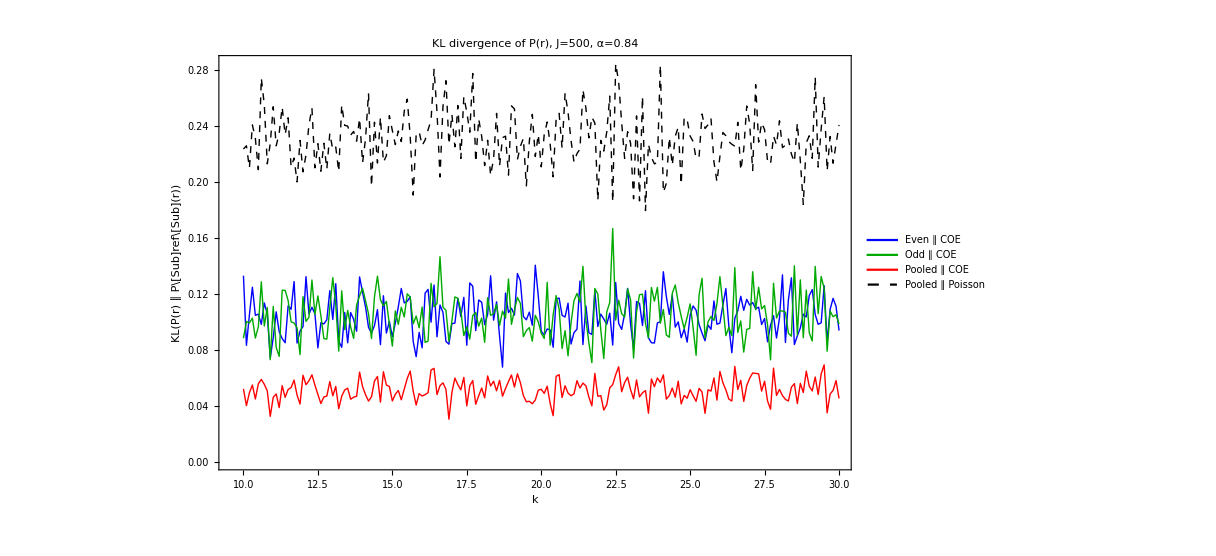

```mathematica
(* === PLOT === *)
kVals = klResults[[All, "k"]];

pOpts = Sequence[Frame -> True, ImageSize -> 900,
  FrameStyle -> Directive[Black, 20], LabelStyle -> Directive[Black, 18]];

plt = Legended[
  ListLinePlot[
    Transpose[{kVals, #}] & /@ {
      klResults[[All, "KL_E_COE"]],
      klResults[[All, "KL_O_COE"]],
      klResults[[All, "KL_All_COE"]],
      klResults[[All, "KL_All_Pois"]]},
    PlotStyle -> {Directive[Blue,Thick], Directive[Darker[Green],Thick],
                  Directive[Red,Thick],  Directive[Black,Thick,Dashed]},
    pOpts,
    FrameLabel -> {"k", "KL(P(r) ∥ P\[Sub]ref\[Sub](r))"},
    PlotLabel -> "KL divergence of P(r),  J=" <> ToString[J] <> ",  α=" <> ToString[alpha],
    PlotRange -> {All, {0, Automatic}}],
  Placed[LineLegend[
    {Directive[Blue,Thick], Directive[Darker[Green],Thick],
     Directive[Red,Thick],  Directive[Black,Thick,Dashed]},
    {"Even ∥ COE", "Odd ∥ COE",
     "Pooled ∥ COE", "Pooled ∥ Poisson"},
    LabelStyle -> Directive[Black, 16]], {Right, Top}]];

Export[FileNameJoin[{outDir, "kl_Pr_vs_k.png"}],
  Rasterize[plt, ImageResolution -> 150, Background -> White]];
Print["Plot saved."];
plt
```

# Second test

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[14];
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Spectral measures analysis\\QKT_full.wl"];
```

```mathematica
(* === PARAMETERS === *)
J     = 500;
alpha = 0.84;
nReal = 50;
delta = 0.001;
nBins = 50;
sMax  = 4.0;
kList = Range[20, 30, 0.1];
```

```mathematica
(* === sx2 EIGENSYSTEM: precomputed once on main kernel === *)
sx2=generateSpinOperators[J]["Sx2"];
{sx2Vals, sx2Vecs} = Eigensystem[N[sx2]];
sx2VecsT = Transpose[sx2Vecs];
freeVec  = Exp[-I alpha Range[J, -J, -1]];
idx      = ParitySectorIndices[J];

TwistFast[k_?NumericQ] :=
  sx2VecsT . (Exp[(-I k / (2. J)) sx2Vals] * sx2Vecs);

FloqSectorFast[k_?NumericQ] :=
  Module[{T = TwistFast[k], idxE = idx["Even"], idxO = idx["Odd"]},
    <|"Even" -> (T[[idxE, idxE]] * freeVec[[idxE]]),
      "Odd"  -> (T[[idxO, idxO]] * freeVec[[idxO]])|>];

GetSpectraFast[k_?NumericQ] :=
  Module[{sectors, eigsE, eigsO, phE, phO, nE, nO},
    sectors = FloqSectorFast[k];
    eigsE   = Eigenvalues[sectors["Even"], Method -> "Direct"];
    eigsO   = Eigenvalues[sectors["Odd"],  Method -> "Direct"];
    phE = Sort[Mod[Arg[eigsE], 2 Pi]]; nE = Length[phE];
    phO = Sort[Mod[Arg[eigsO], 2 Pi]]; nO = Length[phO];
    <|"Even" -> <|"Spectrum" -> (nE / (2 Pi)) phE, "N" -> nE|>,
      "Odd"  -> <|"Spectrum" -> (nO / (2 Pi)) phO, "N" -> nO|>|>];

(* Parallel ensemble using fast Floquet construction *)
GenerateEnsembleFast[kEns_List] :=
  Module[{allSpec},
    DistributeDefinitions[J, alpha, sx2Vals, sx2Vecs, sx2VecsT, freeVec, idx,
      TwistFast, FloqSectorFast, GetSpectraFast];
    allSpec = ParallelTable[GetSpectraFast[k], {k, kEns},
      Method -> "CoarsestGrained"];
    <|"Even" -> allSpec[[All, "Even"]],
      "Odd"  -> allSpec[[All, "Odd"]]|>];
```

Eigensystem::arh: Because finding 1001 out of the 1001 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

```mathematica
(* === REFERENCE BIN PROBABILITIES: precomputed once on main kernel === *)
binWidthS = N[sMax / nBins];
binEdgesS = N[Range[0, sMax, binWidthS]];

coeBinProbS = Normalize[
  MapThread[NIntegrate[WignerCOE[s], {s, #1, #2}] &,
    {Most[binEdgesS], Rest[binEdgesS]}], Total];

poissBinProbS = Normalize[
  MapThread[NIntegrate[Exp[-s], {s, #1, #2}] &,
    {Most[binEdgesS], Rest[binEdgesS]}], Total];
```

```mathematica
(* === WORKER FUNCTIONS: defined on main kernel, then distributed === *)
EmpBinProbS[spacings_List] :=
  N[BinCounts[spacings, {0, sMax, binWidthS}]] / Length[spacings];

KLDiv[p_List, q_List] :=
  Module[{eps = 1.*^-14},
    Total @ MapThread[
      If[#1 < eps, 0., #1 * Log[#1 / Max[#2, eps]]] &, {p, q}]];

DistributeDefinitions[sMax, binWidthS, coeBinProbS, poissBinProbS,
  EmpBinProbS, KLDiv];
```

```mathematica
(* === MAIN LOOP: sequential over k, parallel over the 50 matrices inside === *)
{tTotal, klResults} = AbsoluteTiming[
  Table[
    Module[{kEns, ens, spE, spO, spAll, pE, pO, pAll},
      SeedRandom[];
      kEns  = RandomReal[{k - delta, k + delta}, nReal];
      ens   = GenerateEnsembleFast[kEns];   (* fast; NOT GenerateQKTEnsemble *)
      spE   = Sort @ Flatten[NNSpacings /@ ens["Even"]];
      spO   = Sort @ Flatten[NNSpacings /@ ens["Odd"]];
      spAll = Sort @ Join[spE, spO];
      pE    = EmpBinProbS[spE];
      pO    = EmpBinProbS[spO];
      pAll  = EmpBinProbS[spAll];
      Print["k = ", k, "  (", Length[spAll], " spacings)"];
      <|"k"           -> k,
        "KL_E_COE"    -> KLDiv[pE,   coeBinProbS],
        "KL_O_COE"    -> KLDiv[pO,   coeBinProbS],
        "KL_All_COE"  -> KLDiv[pAll, coeBinProbS],
        "KL_E_Pois"   -> KLDiv[pE,   poissBinProbS],
        "KL_O_Pois"   -> KLDiv[pO,   poissBinProbS],
        "KL_All_Pois" -> KLDiv[pAll, poissBinProbS]|>
    ],
    {k, kList}]
];
Print["Total: ", Round[tTotal, 0.1], " s"];
```

k = 20.  (50050 spacings)

k = 20.1  (50050 spacings)

k = 20.2  (50050 spacings)

k = 20.3  (50050 spacings)

k = 20.4  (50050 spacings)

k = 20.5  (50050 spacings)

k = 20.6  (50050 spacings)

k = 20.7  (50050 spacings)

k = 20.8  (50050 spacings)

k = 20.9  (50050 spacings)

k = 21.  (50050 spacings)

k = 21.1  (50050 spacings)

k = 21.2  (50050 spacings)

k = 21.3  (50050 spacings)

k = 21.4  (50050 spacings)

k = 21.5  (50050 spacings)

k = 21.6  (50050 spacings)

k = 21.7  (50050 spacings)

k = 21.8  (50050 spacings)

k = 21.9  (50050 spacings)

k = 22.  (50050 spacings)

k = 22.1  (50050 spacings)

k = 22.2  (50050 spacings)

k = 22.3  (50050 spacings)

k = 22.4  (50050 spacings)

k = 22.5  (50050 spacings)

k = 22.6  (50050 spacings)

k = 22.7  (50050 spacings)

k = 22.8  (50050 spacings)

k = 22.9  (50050 spacings)

k = 23.  (50050 spacings)

k = 23.1  (50050 spacings)

k = 23.2  (50050 spacings)

k = 23.3  (50050 spacings)

k = 23.4  (50050 spacings)

k = 23.5  (50050 spacings)

k = 23.6  (50050 spacings)

k = 23.7  (50050 spacings)

k = 23.8  (50050 spacings)

k = 23.9  (50050 spacings)

k = 24.  (50050 spacings)

k = 24.1  (50050 spacings)

k = 24.2  (50050 spacings)

k = 24.3  (50050 spacings)

k = 24.4  (50050 spacings)

k = 24.5  (50050 spacings)

k = 24.6  (50050 spacings)

k = 24.7  (50050 spacings)

k = 24.8  (50050 spacings)

k = 24.9  (50050 spacings)

k = 25.  (50050 spacings)

k = 25.1  (50050 spacings)

k = 25.2  (50050 spacings)

k = 25.3  (50050 spacings)

k = 25.4  (50050 spacings)

k = 25.5  (50050 spacings)

k = 25.6  (50050 spacings)

k = 25.7  (50050 spacings)

k = 25.8  (50050 spacings)

k = 25.9  (50050 spacings)

k = 26.  (50050 spacings)

k = 26.1  (50050 spacings)

k = 26.2  (50050 spacings)

k = 26.3  (50050 spacings)

k = 26.4  (50050 spacings)

k = 26.5  (50050 spacings)

k = 26.6  (50050 spacings)

k = 26.7  (50050 spacings)

k = 26.8  (50050 spacings)

k = 26.9  (50050 spacings)

k = 27.  (50050 spacings)

k = 27.1  (50050 spacings)

k = 27.2  (50050 spacings)

k = 27.3  (50050 spacings)

k = 27.4  (50050 spacings)

k = 27.5  (50050 spacings)

k = 27.6  (50050 spacings)

k = 27.7  (50050 spacings)

k = 27.8  (50050 spacings)

k = 27.9  (50050 spacings)

k = 28.  (50050 spacings)

k = 28.1  (50050 spacings)

k = 28.2  (50050 spacings)

k = 28.3  (50050 spacings)

k = 28.4  (50050 spacings)

k = 28.5  (50050 spacings)

k = 28.6  (50050 spacings)

k = 28.7  (50050 spacings)

k = 28.8  (50050 spacings)

k = 28.9  (50050 spacings)

k = 29.  (50050 spacings)

k = 29.1  (50050 spacings)

k = 29.2  (50050 spacings)

k = 29.3  (50050 spacings)

k = 29.4  (50050 spacings)

k = 29.5  (50050 spacings)

k = 29.6  (50050 spacings)

k = 29.7  (50050 spacings)

k = 29.8  (50050 spacings)

k = 29.9  (50050 spacings)

k = 30.  (50050 spacings)

Total: 984.5 s

```mathematica
(* === EXPORT === *)
outDir = FileNameJoin[{NotebookDirectory[], "Results", "KL_Ps"}];
If[!DirectoryQ[outDir], CreateDirectory[outDir, CreateIntermediateDirectories -> True]];
Export[FileNameJoin[{outDir, "kl_Ps_vs_k.wdx"}], klResults, "WDX"];
Print["Saved."];
```

Saved.

Plot saved.

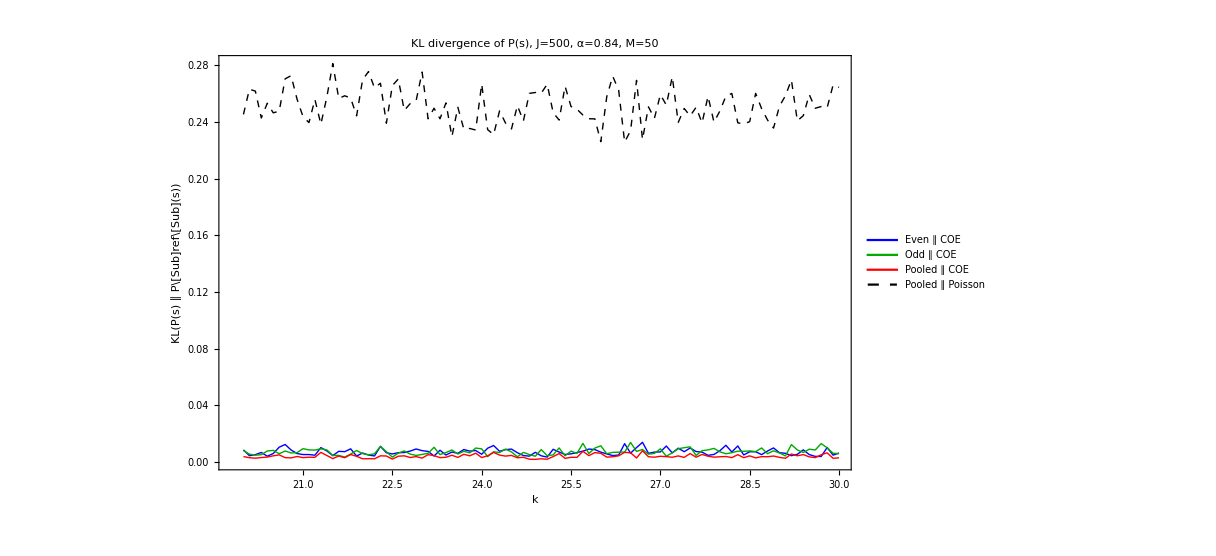

```mathematica
(* === PLOT === *)
kVals = klResults[[All, "k"]];

pOpts = Sequence[Frame -> True, ImageSize -> 900,
  FrameStyle -> Directive[Black, 20], LabelStyle -> Directive[Black, 18]];

plt = Legended[
  ListLinePlot[
    Transpose[{kVals, #}] & /@ {
      klResults[[All, "KL_E_COE"]],
      klResults[[All, "KL_O_COE"]],
      klResults[[All, "KL_All_COE"]],
      klResults[[All, "KL_All_Pois"]]},
    PlotStyle -> {Directive[Blue, Thick], Directive[Darker[Green], Thick],
                  Directive[Red, Thick],  Directive[Black, Thick, Dashed]},
    pOpts,
    FrameLabel -> {"k", "KL(P(s) ∥ P\[Sub]ref\[Sub](s))"},
    PlotLabel -> "KL divergence of P(s),  J=" <> ToString[J] <>
                 ",  α=" <> ToString[alpha] <>
                 ",  M=" <> ToString[nReal],
    PlotRange -> {All, {0, Automatic}}],
  Placed[LineLegend[
    {Directive[Blue, Thick], Directive[Darker[Green], Thick],
     Directive[Red, Thick],  Directive[Black, Thick, Dashed]},
    {"Even ∥ COE", "Odd ∥ COE",
     "Pooled ∥ COE", "Pooled ∥ Poisson"},
    LabelStyle -> Directive[Black, 16]], {Right, Top}]];

Export[FileNameJoin[{outDir, "kl_Ps_vs_k.png"}],
  Rasterize[plt, ImageResolution -> 150, Background -> White]];
Print["Plot saved."];
plt
```